```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Some Graphing Tools *)
myTicks[min_,max_,spacing_,nminor_]:=Module[{minorSpacing=spacing/(nminor+1),majorVals,minorVals,eps=10^-7 spacing},(*Generate Major Ticks*)majorVals=Table[{i,NumberForm[N[i],{Infinity,2},NumberPadding->{"","0"}],{0.02,0}},{i,Ceiling[min/spacing]*spacing,Floor[max/spacing]*spacing,spacing}];
(*Generate Minor Ticks,filtering near-coincident major tick positions*)minorVals=Table[{j,"",{0.01,0}},{j,Ceiling[min/minorSpacing]*minorSpacing,Floor[max/minorSpacing]*minorSpacing,minorSpacing}];
minorVals=Select[minorVals,Function[tick,NoneTrue[majorVals[[All,1]],Abs[#-tick[[1]]]<eps&]]];
Join[majorVals,minorVals]]
Needs["MaTeX`"]
```

```mathematica
(*Narrow resonance V=9, kres=0.5392022503575177-0.09990983772868195 ⅈ..... wide resonance V=2, kres=1.6568773873855651-1.4606098496557252 ⅈ*)
(*Remember we are using a potential V=Spherical well/(2mu) to make the mu dependence go away in the Sch. Eq.*)
a=1;
g=20;
μ=1;
l=1;

kres=4.714304496999773-0.05067937205151212 ⅈ;
kres2=8.063042352489518-0.12815691814454724 ⅈ;
Eres=kres^2/(2μ);

NSolve[1-I*z*g*a^2*SphericalBesselJ[l,z*a]*SphericalHankelH1[l,z*a]==0 && 0<=Re[z]<10 && -10<Im[z]<5,{z}]
NSolve[1+I*z*g*a^2*SphericalBesselJ[l,z*a]*SphericalHankelH2[l,z*a]==0 && -10<=Re[z]<10 && -10<Im[z]<5,{z}]
```

{{z→0.-0.946729 ⅈ},{z→4.7143-0.0506794 ⅈ},{z→8.06304-0.128157 ⅈ}}

{{z→-8.06304+0.128157 ⅈ},{z→-4.7143+0.0506794 ⅈ},{z→0.+0.946729 ⅈ},{z→0.-9.89793 ⅈ},{z→4.7143+0.0506794 ⅈ},{z→8.06304+0.128157 ⅈ}}

```mathematica
(* Exact δ-shell T matrix and λ' modified coupling used in Ψ_U *)
TExact[p_,q_,u_]=-((g*a^2)/(Pi*μ))*(SphericalBesselJ[l,p*a]*SphericalBesselJ[l,q*a])/(1-I*u*g*a^2*SphericalBesselJ[l,u*a]*SphericalHankelH1[l,u*a]);
gprime[u_]=g/(1+I*2*u*g*a^2*(SphericalBesselJ[l,u*a])^2);

(*Define Ψ_U and the Factorized T Matrix Note the -k in λ due to the PsiU function being an eigenvector of -kres*)
Psi[p_,u_]=-4*Pi*g*a^2*SphericalBesselJ[l,p*a]*SphericalBesselJ[l,u*a]/(u^2-p^2);
PsiU[p_,ures_]=-4*Pi*gprime[ures]*a^2*SphericalBesselJ[l,p*a]*SphericalBesselJ[l,ures*a]/(ures^2-p^2);
PsiUTilde[p_,ures_]=(ures^2-p^2)*PsiU[p,ures];
TFactorized[p_,q_,u_,ures_]=(1/(2μ))^2PsiUTilde[p,-ures]*PsiUTilde[q,-ures]/(ures^2-u^2);
```

```mathematica
AbsArgPlot[{TExact[k,k,k],TFactorized[k,k,k,kres]*(TExact[Re[kres],Re[kres],Re[kres]]/TFactorized[Re[kres],Re[kres],Re[kres],kres])},{k,0,10},PlotStyle->{{},{Dashed} },PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All]
```

-Graphics-

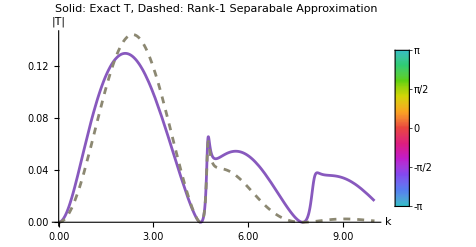

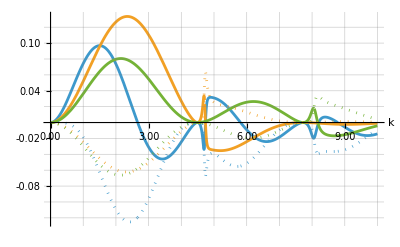

C:\Users\Logan\Mathematica\EFTMathematica\AILumiere1.png

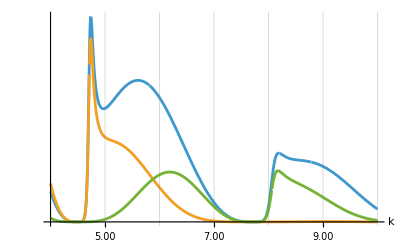

51.8085

-Graphics-

```mathematica
(* Try to work in Position Space (with reduced wavefunction chi!!) and Numerically Normalize*)
ChiUInside[r_,u_]:=r*SphericalBesselJ[l,u*r]*SphericalHankelH1[l,u*a]
ChiUOutside[r_,u_]:=r*SphericalBesselJ[l,u*a]*SphericalHankelH1[l,u*r]

(* <psi|psi> for inner and outer parts *)
NormInsideNumerical[u_?NumericQ]:=NIntegrate[ChiUInside[r,u]^2,{r,0,a},Method->"LocalAdaptive"]
NormOutsideNumerical[u_?NumericQ]:=NIntegrate[ChiUOutside[r,u]^2,{r,a,Infinity},Method->"LocalAdaptive"]

(* <psi|d_E U|psi> *)
(*gprimederiv[u_?NumericQ]:=D[gprime[z],z]/.z->u;*)
DerivativeNormNumerical[u_]:=-(1/(2u))*ChiUInside[a,u]^2*gprime'[u];

(* Total Norm *)
TotalNormNumerical[u_?NumericQ]:=TotalNormNumerical[u]=NormInsideNumerical[u]+NormOutsideNumerical[u]-DerivativeNormNumerical[u]

(* Construct Factorized T Matrix *)
TFactorizedNumerical[p_,q_,u_,ures_]:=gprime[-ures]^2*a^2/(Pi*μ) * ChiUInside[a,-ures]^2/(ures^2-u^2) * (SphericalBesselJ[l,p*a]*SphericalBesselJ[l,q*a])/TotalNormNumerical[-ures];

kmin = 0;
kmax = 10;
AbsArgPlot[{TExact[k,k,k],TFactorizedNumerical[k,k,k,kres]},{k,kmin,kmax},PlotStyle->{{},{Dashed} },PlotLabel->"Solid: Exact T, Dashed: Rank-1 Separabale Approximation",PlotRange->All, AxesLabel->{"k","|T|"},PlotLegends->Automatic,GridLines->{Range[kmin,kmax,(kmax-kmin)/10],Range[0,#2,(#2-#1)/8]&},Ticks->{myTicks[#1,#2,(kmax-kmin)/10,3]&,myTicks[#1,#2,(#2-#1)/4,3]&}]

p= ReImPlot[{TExact[k,k,k],TFactorizedNumerical[k,k,k,kres],TFactorizedNumerical[k,k,k,kres2]},{k,kmin,kmax},PlotStyle->Automatic,PlotRange->All, AxesLabel->{"k",""},PlotLegends->LineLegend[{Directive[ColorData[97][1],Solid],Directive[ColorData[97][1],Dashed],Directive[ColorData[97][2],Solid],Directive[ColorData[97][2],Dashed],Directive[ColorData[97][3],Solid],Directive[ColorData[97][3],Dashed]},{MaTeX["\\text{Re}(T_l(k))"],MaTeX["\\text{Im}(T_l(k))"],MaTeX["\\text{Re}(T^{F,1}_l(k))"],MaTeX["\\text{Im}(T^{F,1}_l(k))"],MaTeX["\\text{Re}(T^{F,2}_l(k))"],MaTeX["\\text{Im}(T^{F,2}_l(k))"]}],GridLines->{Range[kmin,kmax,(kmax-kmin)/10],Range[-0.14,0.14,0.28/14]},
Ticks->{myTicks[#1,#2,(kmax-kmin)/10,3]&,myTicks[-0.14,0.14,0.28/14,3]}]
Export[FileNameJoin[{NotebookDirectory[],"AILumiere1.png"}],Rasterize[p,"Image",ImageResolution->300]]
 Plot[{Abs[TExact[k,k,k]]^2,Abs[TFactorizedNumerical[k,k,k,kres]]^2,Abs[TFactorizedNumerical[k,k,k,kres2]]^2},{k,4,kmax},PlotStyle->Automatic,PlotRange->All, AxesLabel->{"k",""},PlotLegends->LineLegend[{Directive[ColorData[97][1],Solid],Directive[ColorData[97][2],Dashed],Directive[ColorData[97][3],Dotted]},{"","",""}],GridLines->{Range[kmin,kmax,(kmax-kmin)/10],Range[-0.14,0.14,0.28/14]},
Ticks->{myTicks[#1,#2,(kmax-kmin)/10,3]&,myTicks[-0.14,0.14,0.28/14,3]}]

64*Pi^5*3*(Abs[TExact[4.74,4.74,4.74]]^2+Abs[TExact[8.18,8.18,8.18]]^2-Abs[TFactorizedNumerical[4.74,4.74,4.74,kres]]^2-Abs[TFactorizedNumerical[8.18,8.18,8.18,kres2]]^2)

AbsArgPlot[TFactorizedNumerical[k,k,k,kres],{k,kmin,kmax},PlotStyle->{},PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All,GridLines->Automatic]
```

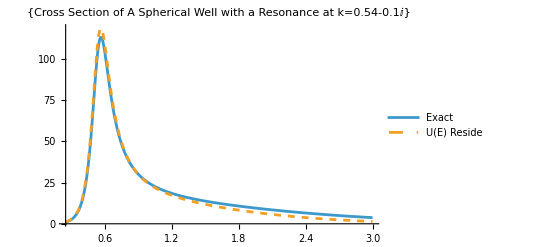

```mathematica
(* Construct the cross section by first getting the inverse K matrix, then making XS from that *)
KMatrixInverseFactorized[u_]:=Re[1/(TFactorizedNumerical[u,u,u,kres])]
KMatrixFactorized[u_]:=1/KMatrixInverseFactorized[u];
XSKMatrixFactorized[u_]:=(64 Pi^5 μ^2)*(2+1)(*(4Pi/p^2)(2L+1)*)*KMatrixFactorized[u]^2/(1+(4*Pi^2*μ*u*KMatrixFactorized[u])^2);

(* Exact cross section *)
XS[u_]:=(64Pi^5μ^2)*(2+1)*Abs[TExact[u,u,u]]^2;
XSFactorized[u_]:=(64Pi^5μ^2)*(2+1)*Abs[TFactorizedNumerical[u,u,u,kres]]^2;

Plot[{XS[z],XSFactorized[z]},{z,0.25,3},PlotStyle->{{},{Dashed}},PlotLabel->{"Cross Section of A Spherical Well with a Resonance at k=0.54-0.1ⅈ"},PlotLegends->{"Exact","U(E) Residue"},PlotRange->All]
```

```mathematica
(* Try to include Born term *)
TBorn[p_,q_]:=1/(2Pi^2)(-V0/(2μ))J[p,q]
SBorn[p_,q_]:=1-8*Pi^2*I*μ*p*TBorn[p,q]
AbsArgPlot[{TExact[k,k,k],TBorn[k,k]+SBorn[k,k]*TFactorizedNumerical[k,k,k,kres],TFactorizedNumerical[k,k,k,kres]},{k,0,10},PlotStyle->{{},{Dashed} ,{Dotted}},PlotLabel->"Solid=Exact T, Dashed=Factorized T",PlotRange->All]
```

-Graphics-

```mathematica
test = 2;
N[TExact[test,test,test]]
(TBorn[test,test]+TFactorizedNumerical[test,test,test,kres])
```

0.00214805-0.0122897 ⅈ

-0.013356+0.0102938 ⅈ

```mathematica
(* Try to include the "hard sphere" term that you get via Hadamards factorization. i.e. S = S_hs * (pole stuff)*)
Shs[p_]:=-SphericalHankelH2[1,p*a]/SphericalHankelH1[1,p*a] (*Shs=e^(2idelta_hs(k)*)
Ths[p_]:=(1-Shs[p])/(8*Pi^2*I*μ*p)

deltabg[p_]:=ArcTan[SphericalBesselJ[l,a*p]/SphericalBesselY[l,a*p]]
Sbg[p_]:=Exp[2*I*deltabg[p]]
Tbg[p_]:=Sin[deltabg[p]]*Exp[I*deltabg[p]]

AbsArgPlot[{TExact[k,k,k],Ths[k]+Shs[k]*TFactorizedNumerical[k,k,k,kres],TFactorizedNumerical[k,k,k,kres]},{k,0,10},PlotStyle->{{},{Dashed} ,{Dotted}},PlotLabel->"Solid=Exact T, Dashed=Factorized T + Hard Sphere, Dotted=Factorized T",PlotRange->All]
```

-Graphics-

```mathematica
NSolve[1-I*8*Pi^2*μ*z*TExact[z,z,z]==0 && 0>=Re[z]>-10 && 10>Im[z]>0,z]
```

{{z→-8.62312+1.90916 ⅈ},{z→-5.08598+1.5349 ⅈ},{z→-0.539202+0.0999098 ⅈ}}